## Inferring the dynamical Ising parameters (J,K) using maximum likelihood methods

### Obtaining the Ising configurations from the metapopulation configurations

Importing data : three consecutive lattice configurations (output of the cpp code):  X_t X_(t+1)X_(t+2)

```mathematica
data1=Import["/Downloads/Metapopulation_and_Inference/state_size_3600_epsilon_0.100000_seed_92474_lambda_0.116200_mcs_2999997.txt","Table"];
data2=Import["/Downloads/Metapopulation_and_Inference/state_size_3600_epsilon_0.100000_seed_92474_lambda_0.116200_mcs_2999998.txt","Table"];
data3=Import["/Downloads/Metapopulation_and_Inference/state_size_3600_epsilon_0.100000_seed_92474_lambda_0.116200_mcs_2999999.txt","Table"];
```

Calculating the size of the lattice L

```mathematica
L=Sqrt[Dimensions[data2][[1]]]
```

60

Converting the one dimensional representation (cpp output) to two dimensional format. X1 , X2 and X3 are the consecutive  lattice configurations of the metapopulation Model A for the dispersal 0.1 and the critical noise 0.1162 (values given in name of the imported file)

```mathematica
X1=Table[data1[[(i-1)L + j,1]],{i,L},{j,L}];
X2=Table[data2[[(i-1)L + j,1]],{i,L},{j,L}];
X3=Table[data3[[(i-1)L + j,1]],{i,L},{j,L}];
```

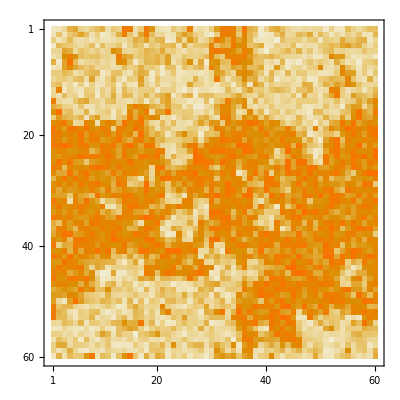
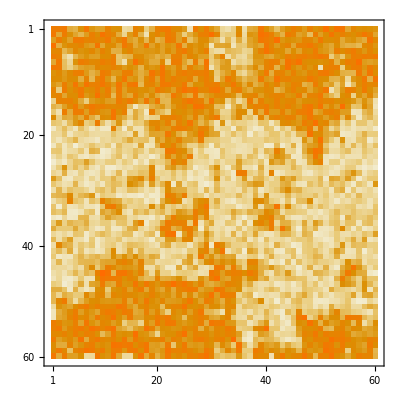
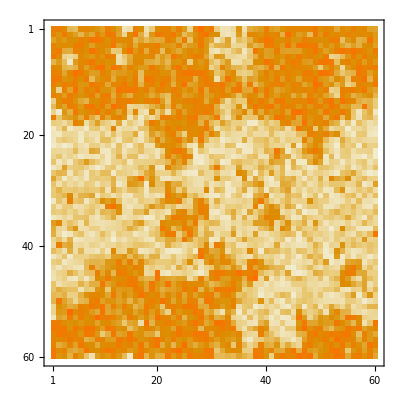

```mathematica
MatrixPlot[X1]MatrixPlot[X2]MatrixPlot[X3]
```

S1 and S2 are the phase configurations of the Metapopulation obtained by the alternating - sign first difference of lattice configurations :(S̃)_t(S̃)_(t+1)

```mathematica
s1=Table[Sign[X2[[i,j]]-X1[[i,j]]],{i,L},{j,L}];
s2=Table[Sign[X2[[i,j]]-X3[[i,j]]],{i,L},{j,L}];
```

Replacing any  zeros  formed due to the function Sign with -1

```mathematica
S1=Table[If[s1[[i,j]]==0,-1,s1[[i,j]]],{i,L},{j,L}];
S2=Table[If[s2[[i,j]]==0,-1,s2[[i,j]]],{i,L},{j,L}];
```

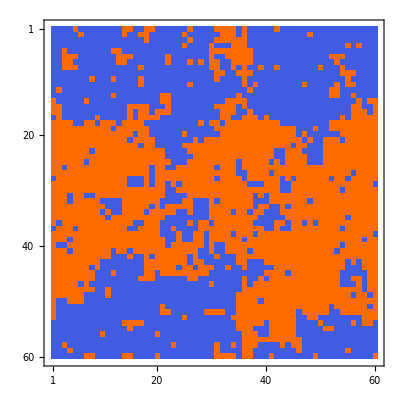
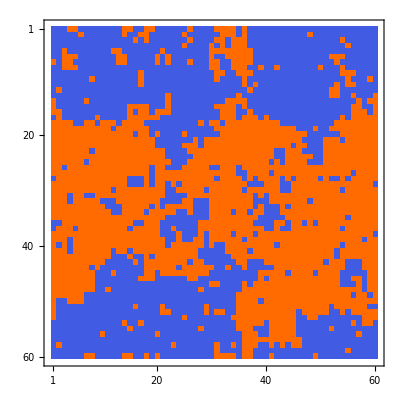

```mathematica
MatrixPlot[S1]MatrixPlot[S2]
```

### Obtaining the ten numbers for inference corresponding to the neighbors and memory at time t and t+1

Extending the phase configurations to include the periodic boundary conditions

```mathematica
s1B=Join[List/@S1[[;;,L]],S1,List/@S1[[;;,1]],2];
S1B=Join[{s1B[[L,;;]]},s1B,{s1B[[1,;;]]}];
s2B=Join[List/@S2[[;;,L]],S2,List/@S2[[;;,1]],2];
S2B=Join[{s2B[[L,;;]]},s2B,{s2B[[1,;;]]}];
```

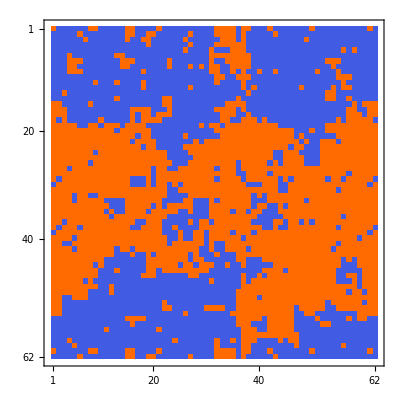
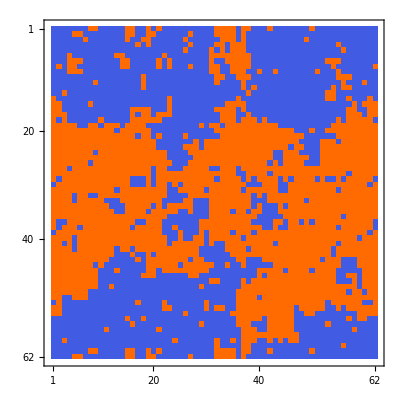

```mathematica
MatrixPlot[S1B]MatrixPlot[S2B]
```

Assigning each spin to a neighborhood corresponding to behavior of neighbors and itself.
neighborhood 1 corresponds to spin S_(t+1) which has (h_t S_t=4 , S_t S_(t+1) =-1) and neighborhood 2 corresponds to  (h_t S_t=4 , S_t S_(t+1) =1)
3 to (h_t S_t=2 , S_t S_(t+1) =-1)
4 to (h_t S_t=2 , S_t S_(t+1) =1) 
5 to (h_t S_t=0 , S_t S_(t+1) =-1) 
6 to (h_t S_t=0 , S_t S_(t+1) =1) 
7 to (h_t S_t=-2 , S_t S_(t+1) =-1) 
8 to (h_t S_t=-2 , S_t S_(t+1) =1) 
9 to (h_t S_t=-4 , S_t S_(t+1) =-1) 
10 to (h_t S_t=-4 , S_t S_(t+1) =1)

```mathematica
F=Table[-(S1B[[i,j+1]]+S1B[[i,j-1]]+S1B[[i+1,j]]+S1B[[i-1,j]])S2B[[i,j]]+6-(-S1B[[i,j]]S2B[[i,j]]+1)/2,{i,2,L+1},{j,2,L+1}];
```

Counting the number of spins in each neighborhood n_hs^f. Same notation followed in the Appendix D 
Number of spins in the given order corresponds to ((n_(hs=4))^f, n_(hs=4) - (n_(hs=4))^f, (n_(hs=2))^f, n_(hs=2) - (n_(hs=2))^f, (n_(hs=0))^f, n_(hs=0) - (n_(hs=0))^f, (n_(hs=-2))^f, n_(hs=-2) - (n_(hs=-2))^f, (n_(hs=-4))^f, n_(hs=-4) - (n_(hs=-4))^f)

```mathematica
n=HistogramList[Flatten[F],{1,11,1}][[2]]
```

{24,2017,16,878,16,374,17,143,20,95}

### Maximizing the likelihood function and finding the parameters

Logarithm of probability for each neighborhood in the same order shown above 
Probability: P=Exp[J h_t S_t+KS_t S_(t+1)]/(2 Cosh[J h_t S_t+KS_t S_(t+1)])
Log probability :   LogP = [J h_t S_t+KS_t S_(t+1)]-Log(2 Cosh[J h_t S_t+KS_t S_(t+1)])

```mathematica
logP={4 J-K-Log[2 Cosh[4 J-K]],4 J+K-Log[2 Cosh[4 J+K]],2 J-K-Log[2 Cosh[2 J-K]],2 J+K-Log[2 Cosh[2 J+K]],-K-Log[2 Cosh[K]],K-Log[2 Cosh[K]],-2 J-K-Log[2 Cosh[2 J+K]],-2 J+K-Log[2 Cosh[2 J-K]],-4 J-K-Log[2 Cosh[4 J+K]],-4 J+K-Log[2 Cosh[4 J-K]]};
```

Likelihood function

```mathematica
L=Total[n logP ]
```

16 (2 J-K-Log[2 Cosh[2 J-K]])+143 (-2 J+K-Log[2 Cosh[2 J-K]])+24 (4 J-K-Log[2 Cosh[4 J-K]])+95 (-4 J+K-Log[2 Cosh[4 J-K]])+16 (-K-Log[2 Cosh[K]])+374 (K-Log[2 Cosh[K]])+17 (-2 J-K-Log[2 Cosh[2 J+K]])+878 (2 J+K-Log[2 Cosh[2 J+K]])+20 (-4 J-K-Log[2 Cosh[4 J+K]])+2017 (4 J+K-Log[2 Cosh[4 J+K]])

Finding maxima of the likelihood function with respect to (J,K)

```mathematica
FindMaximum[Total[L ],{J,K}][[2]]
```

{J→0.205309,K→1.52646}